```mathematica
speedData=Import[NotebookDirectory[]<>"fixed/avespeed2.json"];
```

```mathematica
poiData=Import[NotebookDirectory[]<>"useable/poi_data.json"];
```

```mathematica
expectedSpeed=poiData⟦All,8,2⟧/.{4-> 100,3-> 80,2-> 60,-1->20,1-> 40};
```

```mathematica
plotData=Join[Reverse/@poiData⟦All,7,2⟧,List/@(1-speedData/expectedSpeed),2];
valRange=MinMax[plotData⟦All,3⟧]
GeoGraphics[{
GeoMarker[Most[#],Graphics[{ColorData["ThermometerColors"][Rescale[Last[#],valRange]],Disk[]}],"Scale"-> 0.01]&/@plotData}]
```

{-3.98012,0.840316}

-Graphics-

```mathematica
allSpeed=Table[Import[NotebookDirectory[]<>"useable/avespeed"<>ToString[i]<>".json"],{i,0,6}];
```

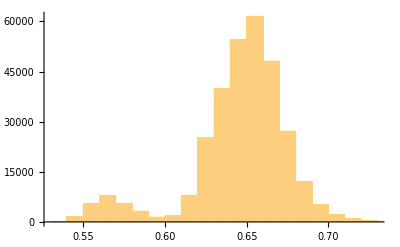

0.0235707

```mathematica
Histogram[Flatten[((expectedSpeed/#/316)^(1/12)&)/@Flatten[allSpeed,1]]]
Min@Flatten[((expectedSpeed/#/316)^(1/2)&)/@Flatten[allSpeed,1]]
```

```mathematica
316
```

315.614

```mathematica
315.61391034534694
```